```mathematica
r1[x_,y_,z_]:=Cos[x]Cos[z]+Sin[x]Sin[y]Sin[z]
```

```mathematica
r2[x_,y_,z_]:=-Sin[x]Cos[z]+Cos[x]Sin[y]Sin[z]
```

```mathematica
r3[x_,y_,z_]:=Cos[y]Sin[z]
```

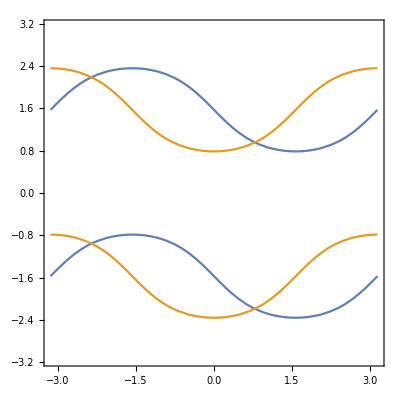

```mathematica
ContourPlot[{r1[0,y,z]==r2[0,y,z],r1[0,y,z]==r3[0,y,z]},{y,-Pi,Pi},{z,-Pi,Pi}]
```

```mathematica
Solve[{r1[0,y,z]==r2[0,y,z],r1[0,y,z]==r3[0,y,z]},{y,z}]
```

{{y→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],z→ConditionalExpression[-ArcTan[√2]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],z→ConditionalExpression[π-ArcTan[√2]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],z→ConditionalExpression[ArcTan[√2]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],z→ConditionalExpression[-π+ArcTan[√2]+2 π C[2],C[2]∈Integers]}}

```mathematica
r1[0,-(3 π)/4,-ArcTan[√2]]
```

1/(√3)

```mathematica
r2[0,-(3 π)/4,-ArcTan[√2]]
```

1/(√3)

```mathematica
r3[0,-(3 π)/4,-ArcTan[√2]]
```

1/(√3)

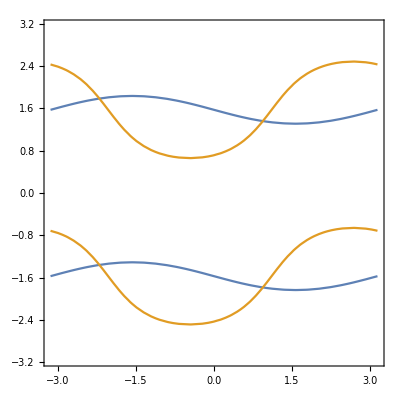

```mathematica
ContourPlot[{r1[Pi/6,y,z]==r2[Pi/6,y,z],r1[Pi/6,y,z]==r3[Pi/6,y,z]},{y,-Pi,Pi},{z,-Pi,Pi}]
```

```mathematica
Solve[{r1[Pi/6,y,z]==r2[Pi/6,y,z],r1[Pi/6,y,z]==r3[Pi/6,y,z]},{y,z}]
```

{{y→ConditionalExpression[ArcTan[1/(√(5-2 √3) (√(3/(5-2 √3))-1/(√(5-2 √3))))]+2 π C[1],C[1]∈Integers],z→ConditionalExpression[-π-ArcTan[((1+√3) √((7+5 √3)/(6+6 √3)))/(√((7+5 √3)/((5-2 √3) (6+6 √3)))-√((3 (7+5 √3))/((5-2 √3) (6+6 √3))))]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[ArcTan[1/(√(5-2 √3) (√(3/(5-2 √3))-1/(√(5-2 √3))))]+2 π C[1],C[1]∈Integers],z→ConditionalExpression[ArcTan[((1+√3) √((7+5 √3)/(6+6 √3)))/(-√((7+5 √3)/((5-2 √3) (6+6 √3)))+√((3 (7+5 √3))/((5-2 √3) (6+6 √3))))]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[-π-ArcTan[1/(√(5-2 √3) (-√(3/(5-2 √3))+1/(√(5-2 √3))))]+2 π C[1],C[1]∈Integers],z→ConditionalExpression[π+ArcTan[((1+√3) √((7+5 √3)/(6+6 √3)))/(√((7+5 √3)/((5-2 √3) (6+6 √3)))-√((3 (7+5 √3))/((5-2 √3) (6+6 √3))))]+2 π C[2],C[2]∈Integers]},{y→ConditionalExpression[-π-ArcTan[1/(√(5-2 √3) (-√(3/(5-2 √3))+1/(√(5-2 √3))))]+2 π C[1],C[1]∈Integers],z→ConditionalExpression[-ArcTan[((1+√3) √((7+5 √3)/(6+6 √3)))/(-√((7+5 √3)/((5-2 √3) (6+6 √3)))+√((3 (7+5 √3))/((5-2 √3) (6+6 √3))))]+2 π C[2],C[2]∈Integers]}}

```mathematica
FullSimplify[r1[Pi/6,ArcTan[1/(√(5-2 √3) (√(3/(5-2 √3))-1/(√(5-2 √3))))],-π-ArcTan[((1+√3) √((7+5 √3)/(6+6 √3)))/(√((7+5 √3)/((5-2 √3) (6+6 √3)))-√((3 (7+5 √3))/((5-2 √3) (6+6 √3))))]]]
```

-1/(√3)

```mathematica
txy[t1_]:={{Cos[t1],Sin[t1],0},{-Sin[t1],Cos[t1],0},{0,0,1}}
```

```mathematica
tyz[t2_]:={{1,0,0},{0,Cos[t2],Sin[t2]},{0,-Sin[t2],Cos[t2]}}
```

```mathematica
tzx[t3_]:={{Cos[t3],0,-Sin[t3]},{0,1,0},{Sin[t3],0,Cos[t3]}}
```

```mathematica
t[t1_,t2_,t3_]:=txy[t1].tyz[t2].tzx[t3]
```

```mathematica
t[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]+Sin[t1] Sin[t2] Sin[t3] | Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]-Cos[t1] Sin[t3]
-Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
Cos[t2] Sin[t3] | -Sin[t2] | Cos[t2] Cos[t3])

```mathematica
t[t1,t2,0]//MatrixForm
```

(Cos[t1] | Cos[t2] Sin[t1] | Sin[t1] Sin[t2]
-Sin[t1] | Cos[t1] Cos[t2] | Cos[t1] Sin[t2]
0 | -Sin[t2] | Cos[t2])

```mathematica
t[t1,Pi/2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]+Sin[t1] Sin[t3] | 0 | Cos[t3] Sin[t1]-Cos[t1] Sin[t3]
-Cos[t3] Sin[t1]+Cos[t1] Sin[t3] | 0 | Cos[t1] Cos[t3]+Sin[t1] Sin[t3]
0 | -1 | 0)

```mathematica
s1[t1_,t2_,t3_]:=Cos[t1] Cos[t3]+Sin[t1] Sin[t2] Sin[t3]+Cos[t2] Sin[t1]
```

```mathematica
s2[t1_,t2_,t3_]:=Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3]+Cos[t1] Cos[t2]
```

```mathematica
s3[t1_,t2_,t3_]:=Cos[t2] Sin[t3]+Sin[t2]
```

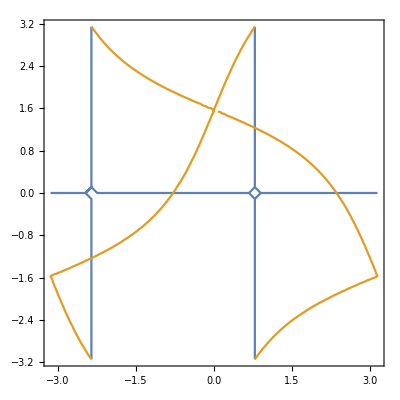

```mathematica
ContourPlot[{s1[t1,t2,0]==s2[t1,t2,0],s1[t1,t2,0]==s3[t1,t2,0]},{t1,-Pi,Pi},{t2,-Pi,Pi}]
```

```mathematica
Solve[{s1[t1,t2,0]==s2[t1,t2,0],s1[t1,t2,0]==s3[t1,t2,0]},{t1,t2}]
```

{{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-ArcTan[2 √2]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[-π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[2 √2]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers]}}

```mathematica
s1[-(3 π)/4,-ArcTan[2 √2],0]
```

-(2 √2)/3

```mathematica
s2[-(3 π)/4,-ArcTan[2 √2],0]
```

-(2 √2)/3

```mathematica
s3[-(3 π)/4,-ArcTan[2 √2],0]
```

-(2 √2)/3

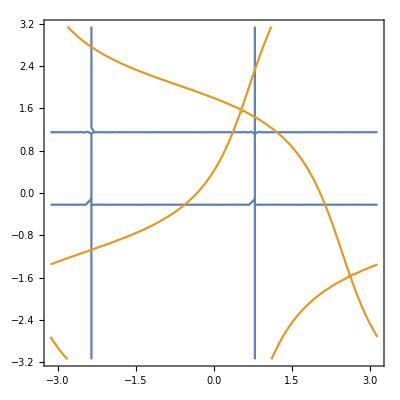

```mathematica
ContourPlot[{s1[t1,t2,Pi/6]==s2[t1,t2,Pi/6],s1[t1,t2,Pi/6]==s3[t1,t2,Pi/6]},{t1,-Pi,Pi},{t2,-Pi,Pi}]
```

```mathematica
Solve[{s1[t1,t2,Pi/6]==s2[t1,t2,Pi/6],s1[t1,t2,Pi/6]==s3[t1,t2,Pi/6]},{t1,t2}]
```

{{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+ArcTan[(119 √3-154 √6+4 √(779+270 √2)+6 √(2 (779+270 √2)))/(7 (-14 √3+√6-√(3116+1080 √2)))]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(119 √3-154 √6-4 √(779+270 √2)-6 √(2 (779+270 √2)))/(7 (-14 √3+√6+√(3116+1080 √2)))]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+ArcTan[(119 √3+154 √6+4 √(779-270 √2)-6 √(2 (779-270 √2)))/(7 (-14 √3-√6-√(3116-1080 √2)))]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(119 √3+154 √6-4 √(779-270 √2)+6 √(2 (779-270 √2)))/(7 (-14 √3-√6+√(3116-1080 √2)))]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[ArcTan[(2-3 √6)/(6+√6)]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(-2 √2+√3)/(√2+2 √3)]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[π+ArcTan[(6+√6)/(2-3 √6)]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(-2 √2+√3)/(√2+2 √3)]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[ArcTan[(6-√6)/(2+3 √6)]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(2 √2+√3)/(-√2+2 √3)]+2 π C[2],C[2]∈Integers]},{t1→ConditionalExpression[ArcTan[(2+3 √6)/(6-√6)]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[(2 √2+√3)/(-√2+2 √3)]+2 π C[2],C[2]∈Integers]}}

```mathematica
N[FullSimplify[s1[-(3 π)/4,π+ArcTan[(119 √3-154 √6+4 √(779+270 √2)+6 √(2 (779+270 √2)))/(7 (-14 √3+√6-√(3116+1080 √2)))],Pi/6]]]
```

-0.0891241

```mathematica
N[FullSimplify[s1[ArcTan[(2+3 √6)/(6-√6)],ArcTan[(2 √2+√3)/(-√2+2 √3)],Pi/6]]]
```

1.11708

```mathematica
result2=Solve[{s1[t1,t2,t3]==s2[t1,t2,t3],s1[t1,t2,t3]==s3[t1,t2,t3],Cos[t2] Sin[t3]==0},{t1,t2,t3}]
```

{{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[-ArcTan[1/(√2 (-1/(√2)+√2))]+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[-π-ArcTan[1/(√2 (1/(√2)-√2))]+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-ArcTan[2 √2]+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π-ArcTan[2 √2]+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+ArcTan[1/(√2 (1/(√2)-√2))]+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[ArcTan[1/(√2 (-1/(√2)+√2))]+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[ArcTan[2 √2]+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[π/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-π+ArcTan[2 √2]+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers],t3→ConditionalExpression[2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-π-ArcTan[1/(√2 (1/(√2)-√2))]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[-π/4+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[-π-ArcTan[1/(√2 (1/(√2)-√2))]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[-(3 π)/4+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[ArcTan[1/(√2 (-1/(√2)+√2))]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[-π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[(3 π)/4+2 π C[3],C[3]∈Integers]},{t1→ConditionalExpression[ArcTan[1/(√2 (-1/(√2)+√2))]+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[π/2+2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π/4+2 π C[3],C[3]∈Integers]}}

```mathematica
Length[result2]
```

20

```mathematica
result2[[1]]
```

{t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers],t2→ConditionalExpression[2 π C[2],C[2]∈Integers],t3→ConditionalExpression[π+2 π C[3],C[3]∈Integers]}

```mathematica
result2[[1]][[1]]
```

t1→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈Integers]

```mathematica
Simplify[s1[t1,t2,t3]/.result2]
```

{ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-(2 √2)/3,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[(2 √2)/3,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[(2 √2)/3,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-(2 √2)/3,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[0,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[-1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers],ConditionalExpression[1,C[1]∈Integers&&C[2]∈Integers&&C[3]∈Integers]}

```mathematica
result1=Solve[{r1[t1,t2,t3]==r2[t1,t2,t3],r1[t1,t2,t3]==r3[t1,t2,t3]},{t1,t2,t3}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]-√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (-√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→-ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[-(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→-ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]},{t1→ArcCos[1/2 (√(1-Cos[t2]^2) Sec[t2]+√(-1+3 Cos[t2]^2) Sec[t2])],t3→ArcCos[(√(-1+3 Cos[t2]^2) Sec[t2])/(√3)]}}

```mathematica
Length[result1]
```

32

```mathematica
result11=FullSimplify[r1[t1,t2,t3]/.result1]
```

{1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))+2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))-2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),1/(2 √3)(-3+Sec[t2]^2 (1-√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(3+Sec[t2]^2 (-1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))-2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))+2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),-1/(2 √3)(3+Sec[t2]^2 (-1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1-√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(3-Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))-√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(3-Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))-√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))-√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(3-Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))-√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(-3+Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(3-Sec[t2]^2 (1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2+√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1-√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),-1/(2 √3)(3+Sec[t2]^2 (-1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))+2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))-2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),-1/(2 √3)(3+Sec[t2]^2 (-1+√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(2 √3)(-3+Sec[t2]^2 (1-√(-1+3 Cos[t2]^2) √(Sin[t2]^2))+√(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))-2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2),1/(4 √3)(3+Sec[t2]^2 (1+2 √(-1+3 Cos[t2]^2) √(Sin[t2]^2))+2 √(Sec[t2]^2) Sin[t2] √(2-√(2+6 Cos[2 t2]) Sec[t2]^2 √(Sin[t2]^2))-3 Tan[t2]^2)}

```mathematica
FullSimplify[result11/.t2->0]
```

{1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3),-1/(√3),-1/(√3),1/(√3),1/(√3)}

```mathematica
FullSimplify[result11/.t2->Pi/6]
```

{(2+√5)/(3 √3),1/(√3),-1/(√3),-(2+√5)/(3 √3),1/(√3),(2+√5)/(3 √3),-(2+√5)/(3 √3),-1/(√3),1/(√3),-(-2+√5)/(3 √3),(-2+√5)/(3 √3),-1/(√3),-(-2+√5)/(3 √3),1/(√3),-1/(√3),(-2+√5)/(3 √3),(-2+√5)/(3 √3),-1/(√3),1/(√3),-(-2+√5)/(3 √3),-1/(√3),(-2+√5)/(3 √3),-(-2+√5)/(3 √3),1/(√3),-1/(√3),-(2+√5)/(3 √3),(2+√5)/(3 √3),1/(√3),-(2+√5)/(3 √3),-1/(√3),1/(√3),(2+√5)/(3 √3)}

```mathematica
FullSimplify[result11/.t2->Pi/12]
```

{4-2 √3+√(-83/3+16 √3),1/(√3),-1/(√3),-4+2 √3-√(-83/3+16 √3),1/(√3),4-2 √3+√(-83/3+16 √3),-4+2 √3-√(-83/3+16 √3),-1/(√3),1/(√3),4-2 √3-√(-83/3+16 √3),-4+2 √3+√(-83/3+16 √3),-1/(√3),4-2 √3-√(-83/3+16 √3),1/(√3),-1/(√3),-4+2 √3+√(-83/3+16 √3),-4+2 √3+√(-83/3+16 √3),-1/(√3),1/(√3),4-2 √3-√(-83/3+16 √3),-1/(√3),-4+2 √3+√(-83/3+16 √3),4-2 √3-√(-83/3+16 √3),1/(√3),-1/(√3),-4+2 √3-√(-83/3+16 √3),4-2 √3+√(-83/3+16 √3),1/(√3),-4+2 √3-√(-83/3+16 √3),-1/(√3),1/(√3),4-2 √3+√(-83/3+16 √3)}

```mathematica
N[result11/.t2->Pi/24]
```

{0.67437,0.57735,-0.57735,-0.67437,0.57735,0.67437,-0.67437,-0.57735,0.57735,0.460316,-0.460316,-0.57735,0.460316,0.57735,-0.57735,-0.460316,-0.460316,-0.57735,0.57735,0.460316,-0.57735,-0.460316,0.460316,0.57735,-0.57735,-0.67437,0.67437,0.57735,-0.67437,-0.57735,0.57735,0.67437}

```mathematica
N[1/Sqrt[3]]
```

0.57735

```mathematica
N[result11/.t2->3Pi/16]
```

{0.800416,0.57735,-0.57735,-0.800416,0.57735,0.800416,-0.800416,-0.57735,0.57735,-0.161246,0.161246,-0.57735,-0.161246,0.57735,-0.57735,0.161246,0.161246,-0.57735,0.57735,-0.161246,-0.57735,0.161246,-0.161246,0.57735,-0.57735,-0.800416,0.800416,0.57735,-0.800416,-0.57735,0.57735,0.800416}